```mathematica
<<Radia`;
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

```mathematica
B={{-30, -30},{-30,30},{30,30},{30,-30}};
Mmax=1;
mh0[s_]=Mmax*{0,Sin[(2π)/λu s],Cos[(2π)/λu s]};
λu=240.;
wm=λu/4.;
Np= 3;
pos=wm Range[0,4Np-1];
mh0[#]&/@pos
```

{{0,0.,1.},{0,1.,6.12323×10^-17},{0,1.22465×10^-16,-1.},{0,-1.,-1.83697×10^-16},{0,-2.44929×10^-16,1.},{0,1.,3.06162×10^-16},{0,3.67394×10^-16,-1.},{0,-1.,-4.28626×10^-16},{0,-4.89859×10^-16,1.},{0,1.,5.51091×10^-16},{0,6.12323×10^-16,-1.},{0,-1.,-2.44991×10^-15}}

```mathematica
radUtiDelAll[];

core=radObjRecMag[{RegionCentroid[Polygon[B]][[1]],#,RegionCentroid[Polygon[B]][[2]]},{60,wm,60},mh0[#]]&/@pos;
HC=radObjCnt[Flatten[{core}]];
```

```mathematica
RadPlot3DOptions[];
dr=radObjDrw[HC];
Show[Graphics3D[dr,PlotLabel->"Block",BaseStyle -> {14, FontFamily -> "Times"}]]
```

-Graphics3D-

```mathematica
Table[ y,{y,0,Np* λu, 50}]
```

```mathematica
{0,50,100,150,200,250,300,350,400,450,500,550,600,650,700}
```

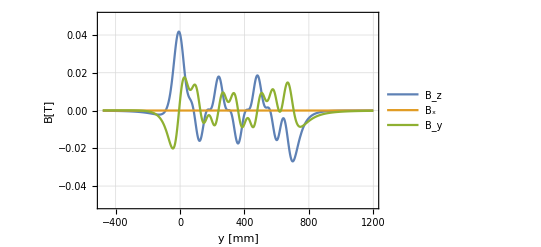

{-2.20951×10^-13,3.57901×10^-14,-3.02753×10^-13,-2.57616×10^-13,3.071×10^-14,4.99259×10^-14,2.47306×10^-13,5.42788×10^-13,2.95191×10^-13,-3.29011×10^-13,-3.49941×10^-13,-1.97919×10^-13,-4.58088×10^-14,-2.74853×10^-14,-1.69983×10^-14}

{0.0405076,0.0083399,-0.00894114,-0.00530515,0.00257699,0.0162267,0.000217665,-0.0157138,-0.00177199,0.0068723,0.0125786,0.00144624,-0.015643,-0.00533539,-0.0269194}

{0.00546705,0.012674,0.012659,-0.00648622,-0.00585264,0.0058339,0.00452557,0.00533019,-0.00701575,-0.00869857,0.00863625,0.00621985,0.00458968,0.0101802,0.0029232}

```mathematica
x = 0;
z =80;
Plot[{radFld[HC,"Bz",{x,y,z}],radFld[HC,"Bx",{x,y, z}],radFld[HC,"By",{x,y,z}]},{y,-2λu,(Np+2) λu},PlotRange-> {All,{-0.05,0.05}},PlotTheme->"Detailed",FrameLabel->{"y [mm]","B[T]"},PlotLegends-> {"B_z","B_x","B_y"}]
Table[radFld[HC,"Bx",{x,y,z}],{y,0,Np* λu, 50}]
Table[radFld[HC,"Bz",{x,y,z}],{y,0,Np* λu, 50}]
Table[radFld[HC,"By",{x,y,z}],{y,0,Np* λu, 50}]
```

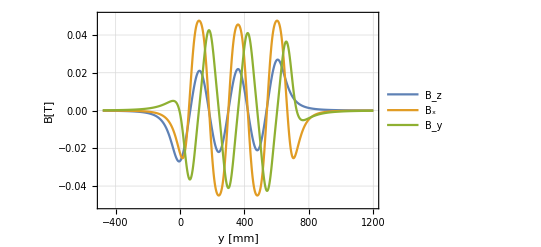

{-0.0226758,-0.00489369,0.044503,0.036577,-0.0253073,-0.0441145,0.000217665,0.0446275,0.0261123,-0.0350098,-0.0408655,0.0146798,0.0475404,0.0195372,-0.0249289}

{-0.0266858,-0.00746262,0.017664,0.0145277,-0.0107684,-0.021125,3.07704×10^-11,0.021125,0.0107684,-0.0145277,-0.017664,0.00746262,0.0266858,0.0179687,0.00708484}

{-0.00168676,-0.0343909,-0.0143576,0.0282643,0.0351816,-0.00811031,-0.0410186,-0.00861402,0.0340185,0.0260519,-0.0183804,-0.0408451,-0.00256413,0.0350098,0.0138426}

```mathematica
x =80;
z =0;
Plot[{radFld[HC,"Bz",{x,y,z}],radFld[HC,"Bx",{x,y, z}],radFld[HC,"By",{x,y,z}]},{y,-2λu,(Np+2) λu},PlotRange-> {All,{-0.05,0.05}},PlotTheme->"Detailed",FrameLabel->{"y [mm]","B[T]"},PlotLegends-> {"B_z","B_x","B_y"}]
Table[radFld[HC,"Bx",{x,y,z}],{y,0,Np* λu, 50}]
Table[radFld[HC,"Bz",{x,y,z}],{y,0,Np* λu, 50}]
Table[radFld[HC,"By",{x,y,z}],{y,0,Np* λu, 50}]
```

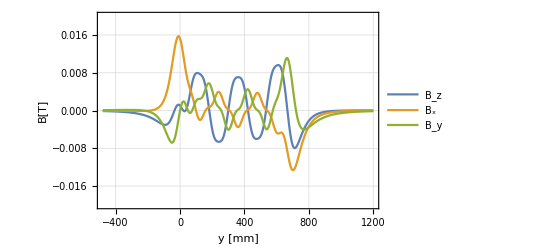

{0.0152391,0.00598453,-0.000169148,-0.000543675,0.00130898,0.00361466,0.000179062,-0.00319731,-0.000674216,0.0017153,0.00265148,-0.000348865,-0.00469498,-0.00599931,-0.0126371}

{0.00101195,0.00157591,0.00789794,0.00624498,-0.00404745,-0.00655362,0.000179062,0.00697097,0.00468221,-0.00507335,-0.00541561,0.00405975,0.00953216,0.00495907,-0.00741171}

{7.07616×10^-6,-0.0000530573,0.0020432,0.00376244,0.00419853,0.000316243,-0.00406323,-0.000122501,0.00321333,0.00199557,-0.000802507,-0.00343124,0.00231925,0.0100653,0.0048441}

```mathematica
x =70;
z =70;
Plot[{radFld[HC,"Bz",{x,y,z}],radFld[HC,"Bx",{x,y, z}],radFld[HC,"By",{x,y,z}]},{y,-2λu,(Np+2) λu},PlotRange-> {All,{-0.02,0.02}},PlotTheme->"Detailed",FrameLabel->{"y [mm]","B[T]"},PlotLegends-> {"B_z","B_x","B_y"}]
Table[radFld[HC,"Bx",{x,y,z}],{y,0,Np* λu, 50}]
Table[radFld[HC,"Bz",{x,y,z}],{y,0,Np* λu, 50}]
Table[radFld[HC,"By",{x,y,z}],{y,0,Np* λu, 50}]
```

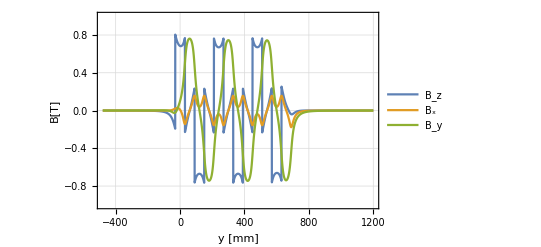

{0.00836054,-0.0419406,0.106722,0.155698,-0.108271,-0.0548864,0.0000607904,0.0550328,0.108515,-0.155169,-0.105225,0.0481118,0.0394214,0.0472075,-0.132158}

{0.683818,-0.0685922,-0.705777,-0.76648,-0.148807,0.677128,0.0000303954,-0.677055,0.148929,-0.233256,0.706525,0.0716736,-0.661014,0.107039,-0.0366783}

{0.101687,0.746518,0.254985,-0.46051,-0.648645,0.107875,0.745336,0.107234,-0.650206,-0.463836,0.247288,0.724067,-0.0025076,-0.723908,-0.252509}

```mathematica
x =20;
z =10;
Plot[{radFld[HC,"Bz",{x,y,z}],radFld[HC,"Bx",{x,y, z}],radFld[HC,"By",{x,y,z}]},{y,-2λu,(Np+2) λu},PlotRange-> {All,{-1,1}},PlotTheme->"Detailed",FrameLabel->{"y [mm]","B[T]"},PlotLegends-> {"B_z","B_x","B_y"}]
Table[radFld[HC,"Bx",{x,y,z}],{y,0,Np* λu, 50}]
Table[radFld[HC,"Bz",{x,y,z}],{y,0,Np* λu, 50}]
Table[radFld[HC,"By",{x,y,z}],{y,0,Np* λu, 50}]
```